```mathematica
SymbolReplace[sym_,edge_]:=Block[{s},
s=SymbolToSets[sym];
s=Map[Flatten[(#/.edge[[1]]->{edge[[1]],edge[[2]]})]&,s];
SetsToSymbol[s]
]
```

```mathematica
JoinGraphs[f_,g_,h_]:=Block [{edges,full},
edges=Join[
Table[e->Directive[{Thick,Red}],{e,EdgeList[f]}],
Table[e->Directive[{Thick,Yellow}],{e,SetDifference[SetDifference[EdgeList[g],EdgeList[f]],EdgeList[h]]}],
Table[e->Directive[{Thick,Blue}],{e,EdgeList[h]}]
];
full=GraphUnion[f,g,h];
Graph[full,VertexLabels->Table[v->Rotate[SymbolToLabel[v],Pi/6],{v,VertexList[full]}],EdgeStyle->edges,
VertexStyle->Join[
Table[v->Red,{v,VertexList[f]}],
Table[v->Blue,{v,VertexList[h]}]],
GraphLayout->"LayeredDigraphEmbedding",
ImageSize->400
]
]
```

```mathematica
FindFullFormula12345[g_]:=Block[{},
Monitor[
formulaDepth=0;FindFullFormula12345[g,Table[{v},{v,VertexList[g]}]],
formulaDepth
]
]
```

```mathematica
FindFullFormula12345[g_,v_]:=Block[{edge,pos1,pos2,v2,result={},result1,result2,clique},
If[CompleteGraphQ[g],
result=Select[{SetsToSymbol2[Sort[Map[Sort[#]&,v],#1[[1]]<#2[[1]]&]]},SymbolLevel[#]≤5&]
,
clique=First[FindClique[g]];
If[Length[clique]≤5,
edge=First[EdgeList[GraphComplement[g]]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
result=Join[
FindFullFormula12345[EdgeAdd[g,edge],v],
FindFullFormula12345[VertexContract[g,{edge[[1]],edge[[2]]}],v2]
]
,
{}
]
];
If[Length[result]>formulaDepth,formulaDepth=Length[result]];
result
]
```

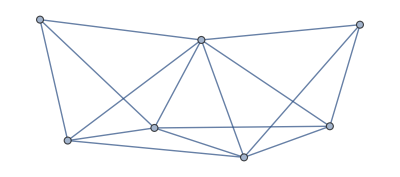
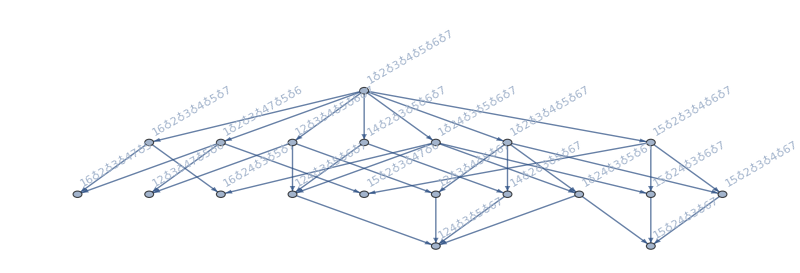
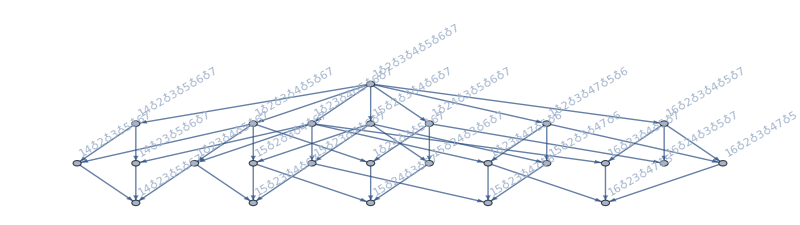
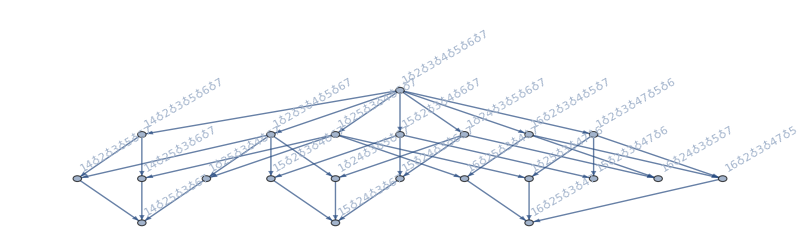
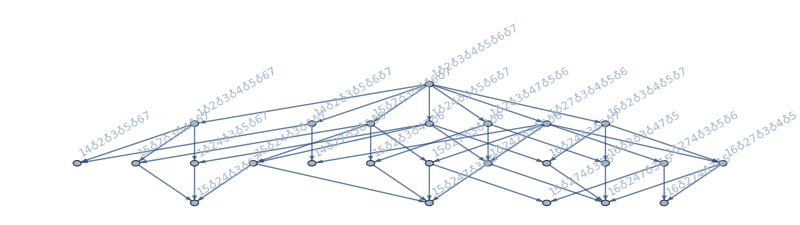
-Graphics-k→{-Graphics-1<->2,-Graphics-2<->3,-Graphics-2<->5,-Graphics-2<->7}

```mathematica
Monitor[
With[{g=ReadGrof[5]},
Block[{edges,full},
edges=DeleteDuplicates[EdgeList[g],IsomorphicGraphQ[EdgeContract[g,#1],EdgeContract[g,#2]]&];
Labeled[g,k]->
Table[Labeled[
Graph[
JoinGraphs[
FormulaGraphReverse2[FindFullFormula[g]],
FormulaGraphReverse2[FindFullFormula[EdgeDelete[g,e]]],
FormulaGraphReverse2[Map[SymbolReplace[#,e]&,FindFullFormula[EdgeContract[g,e]]]]
],ImageSize->800
],e],{e,edges}]
]
],
e]
```

```mathematica
ChromaticPolynomial[Graph[plantri[[1]]],3]
```

0